Quantum Oracle

Classical Oraclepaclet:Q3/tutorial/QuantumOracle#2114503066 | Examplespaclet:Q3/tutorial/QuantumOracle#461755365
Quantum Oraclepaclet:Q3/tutorial/QuantumOracle#466610273 |

See also Section 4.2 of the Quantum Workbook (2022)https://doi.org/10.1007/978-3-030-91214-7.

An oracle in computer science is a “black box” entity that is able to produce a solution for any instance of a given problem without revealing how the solution was obtained.  That being the case, the details of its implementation and its complexity are disregarded. Oracles are commonly used in computer science to theoretically classify problems in computational complexity theory, to analyze the complexity of algorithms, or to provide a way to solve problems. The concept of an oracle (i.e., black box) is a powerful tool in many other sciences as well that enables us to concentrate on what a device does without worrying about how to it is accomplished. In a decision problem, such as the Deutsch-Jozsa and related problems, we are supposed to figure out the unknown property by making queries to the oracle.

In this document, we examine a quantum oracle, i.e., a quantum mechanical implementation of oracle.

Oraclepaclet:Q3/ref/OracleQ3 Package Symbol | Represents a quantum implementation of classical oracle.
ControlledPowerpaclet:Q3/ref/ControlledPowerQ3 Package Symbol | Controlled exponentiation of a unitary gate

Q3 functions related to quantum oracle.

Make sure that the Q3 package is loaded to use the demonstrations in this document.

```mathematica
<<Q3`
```

Throughout this document, symbol S will be used to denote qubits and Pauli operators on them. Similarly, symbol c will be used to denote complex-valued coefficients.

```mathematica
Let[Qubit,S]
Let[Complex,c]
```

Classical Oracle

An oracle (more specifically, classical oracle, to be distinguished from quantum oracle) is typically described by a binary function

f:{0,1}^m→{0,1}^n,

that maps an m-bit input to an n-bit output, and is depicted diagrammatically  in Figure 1. The query model of computation is to solve a problem on an unknown function f, and the oracle is the key entity of the model. Bear in mind that the function f(x) may not be invertible in general.

-Graphics-

Figure 1. A circuit diagram of classical oracle f:{0,1}^m→{0,1}^n. x is an m-bit string (x∈{0,1}^m), and z denotes the image of function f at x (z=f(x)∈{0,1}^n).

Given a classical oracle f, a proper quantum implementation should operate on qubits and allow superposition in the input states. One naive approach is to define an operator O by Ox=f(x) for any state in the computational basis of the m-qubit register. This would not work because, as mentioned above, the function f(x) is not invertible in general, and hence operator O cannot be unitary.

To overcome such an issue, first extend the mapping f by adding an auxiliary register of n bits to the native register and keeping the original input value so that both the input and output registers have (m+n) bits. An extended mapping, {0,1}^(m+n)→{0,1}^(m+n), is then defined by the association (see Figure 2)

(x,y)↦(x,f(x)⊕y) ,

where x∈{0, 1}^m and y∈{0, 1}^n are bit strings of the m-bit native register and the n-bit auxiliary register, respectively.

Figure 2. A reversible version of classical oracle f:{0,1}^m→{0,1}^n.  x∈{0,1}^m and y∈{0,1}^n are m-bit and n-bit strings, respectively, and z=f(x)∈{0,1}^n denotes the image of f at x.

Although the function f(x) itself may not be invertible, the extended mapping above  is always one-to-one regardless of the function f(x). Due to this property, the extended mapping  is widely used to convert a classical code to a form that is suitable for (classical) reversible computation. (For a complete reversible computation, there is another important step required to remove the “garbage” bits.)

Quantum Oracle

### Definition

The quantum oracle corresponding to the classical oracle f is simply an implementation of the above extended mapping for reversible computation on quantum registers. It is a quantum gate operation defined by the association

U_f:x⊗y↦x⊗f(x)⊕y ,

where x and y are the computational basis states belonging to the native and auxiliary register of m and n qubits, respectively. The values of the auxiliary qubits are flipped conditionally depending on the function value f(x) at the corresponding bit value x of the native qubits. In quantum circuit model, a quantum oracle is depicted diagrammatically as shown in Figure 3. Since the extended mapping is one-to-one and the computational basis states are orthonormal, the operator U_f is unitary. Recall that U_f is a linear operator and can act on any arbitrary superposition states.

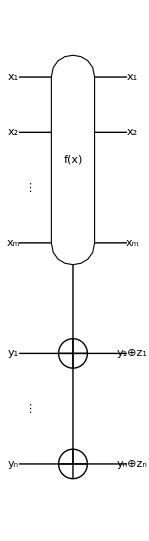

Figure 3. A quantum circuit for the quantum oracle corresponding to classical oracle f:{0,1}^m→{0,1}^n., which is a direct analogue of the classical reversible oracle in Figure 2.  x∈{0,1}^m and y∈{0,1}^n is m-bit and n-bit strings, respectively, and z=f(x)∈{0,1}^n denotes the image of f at x.

### Properties

There are several interesting features of a quantum oracle that can be immediately noticed from the definition above. We note that the CNOT gate makes a copy of the computational basis state of the control register to the target register when the latter has been prepared initially in the state 0,

x⊗0↦x⊗x.

This property illustrated in Figure 3 (right) is exploited in many applications, especially to generate entanglement.

The quantum oracle has a similar property, but it makes a copy of the image f(x) rather than the input state x itself of the native register to the ancillary register,

x⊗0↦x⊗f(x).

This is demonstrated in  in Figure 4 (left).

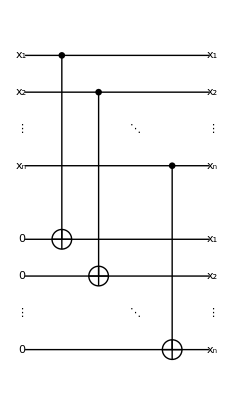
-Graphics-	            -Graphics-

Figure 4. (left) A quantum circuit demonstrating the feature x⊗0↦x⊗f(x) of the quantum oracle corresponding to classical oracle f:{0,1}^m→{0,1}^n. (right) A quantum circuit demonstrating the feature x⊗0↦x⊗x of the CNOT gates.

Furthermore, suppose that a native quantum register is in the superposition

1/2^(m/2)Σ_(x=0)^(2^m-1)x

and the ancillary quantum register in in the state 0≡0^(⊗n). The quantum oracle transforms the state as

1/2^(m/2)Σ_(x=0)^(2^m-1)x⊗0↦1/2^(m/2)Σ_(x=0)^(2^m-1)x⊗f(x)

Just like the CNOT gate, the above state from the quantum oracle is also entangled in general unless f is a constant or very special function. In this case, the entanglement is controlled by the (classical) oracle f.

Recall that the controlled-unitary gate induces a phase shift on the control register (rather than on the target register) when the target register is in an eigenstate of the unitary operator. A similar method can be used to induce a phase shift conditionally on every term that satisfies a certain condition. For example, let f:{0, 1}^n→{0, 1} be a classical oracle, and suppose that we are given a state

ψ=Σ_(x=0)^(2^n-1)x ψ_x

on an n-qubit register. We want to get a new state where every term x satisfying f(x)=1 flips its amplitude ψ_x to -ψ_x

ψ'=Σ_(x=0)^(2^n-1)(x(-1))^(f(x))ψ_x .

In other words, we want an effective quantum gate that maps the computational basis states as

x↦(x(-1))^(f(x))

for x=0,1,2,…,2^n-1. This can be achieved using the quantum oracle corresponding to the function f and preparing an auxiliary qubit in the state -:=(0-1)/(√2), the eigenstate of the Pauli X operator belonging to the eigenvalue −1, as depicted in the quantum circuit in Figure 5. Indeed, for a computational state x with f(x)=1,

x⊗-=(x⊗0-x⊗1)/(√2)↦(x⊗1-x⊗0)/(√2)=-x⊗- ,

while nothing happens for x with f(x)=0.

-Graphics-

Figure 5. A quantum circuit to induces conditional phase shifts depending on function value f(x) at input value x:=(x_1,x_2,…,x_n).

The above feature is widely used in various quantum algorithms including the Deutsch-Jozsa algorithm, Bernstein-Vazirani algorithm, Simon's algorithm, and quantum search algorithm. It is also possible to construct more  general conditional phase shifts.

Examples

```mathematica
<<Q3`
```

```mathematica
Let[Qubit,S]
Let[Complex,c]
```

### For Deutsch-Jozsa Algorithm

Here is a simple example, which is used in the Deutsch-Jozsa algorithm.

Consider a balanced function f as a classical oracle.

```mathematica
Clear[f];
f[{0,0}]=f[{1,1}]=0;
f[{0,1}]=f[{1,0}]=1;
```

Here is the corresponding quantum oracle.

```mathematica
cc=S@{1,2};
tt=S[3];
qc=QuantumCircuit[Oracle[f,cc,tt]]
```

-Graphics-

```mathematica
op=ExpressionFor[qc]
```

1/2+1/2 S_1^ZS_2^Z-1/2 S_1^ZS_2^ZS_3^X+S_3^X/2

```mathematica
in=Basis@Join[cc,{tt}]
```

{0_S_10_S_20_S_3,0_S_10_S_21_S_3,0_S_11_S_20_S_3,0_S_11_S_21_S_3,1_S_10_S_20_S_3,1_S_10_S_21_S_3,1_S_11_S_20_S_3,1_S_11_S_21_S_3}

```mathematica
out=op**in
```

{0_S_10_S_20_S_3,0_S_10_S_21_S_3,0_S_11_S_21_S_3,0_S_11_S_20_S_3,1_S_10_S_21_S_3,1_S_10_S_20_S_3,1_S_11_S_20_S_3,1_S_11_S_21_S_3}

```mathematica
Thread[in->out]//TableForm
```

0_S_10_S_20_S_3→0_S_10_S_20_S_3
0_S_10_S_21_S_3→0_S_10_S_21_S_3
0_S_11_S_20_S_3→0_S_11_S_21_S_3
0_S_11_S_21_S_3→0_S_11_S_20_S_3
1_S_10_S_20_S_3→1_S_10_S_21_S_3
1_S_10_S_21_S_3→1_S_10_S_20_S_3
1_S_11_S_20_S_3→1_S_11_S_20_S_3
1_S_11_S_21_S_3→1_S_11_S_21_S_3

### For Simon's Algorithm

Let us consider another example, which is used in Simon’s algorithm.

Consider a two-to-one function as a classical oracle.

```mathematica
Clear[f];
f[{0,0}]=f[{1,1}]={0,1};
f[{0,1}]=f[{1,0}]={1,1};
```

Here is an implementation of the corresponding quantum oracle.

```mathematica
cc=S@{1,2};
tt=S@{3,4};
qc=QuantumCircuit[Oracle[f,cc,tt]]
```

-Graphics-

```mathematica
op=Elaborate@Oracle[f,cc,tt]
```

1/2 S_3^XS_4^X+1/2 S_1^ZS_2^ZS_4^X-1/2 S_1^ZS_2^ZS_3^XS_4^X+S_4^X/2

```mathematica
in=Basis@Join[cc,tt]
```

{0_S_10_S_20_S_30_S_4,0_S_10_S_20_S_31_S_4,0_S_10_S_21_S_30_S_4,0_S_10_S_21_S_31_S_4,0_S_11_S_20_S_30_S_4,0_S_11_S_20_S_31_S_4,0_S_11_S_21_S_30_S_4,0_S_11_S_21_S_31_S_4,1_S_10_S_20_S_30_S_4,1_S_10_S_20_S_31_S_4,1_S_10_S_21_S_30_S_4,1_S_10_S_21_S_31_S_4,1_S_11_S_20_S_30_S_4,1_S_11_S_20_S_31_S_4,1_S_11_S_21_S_30_S_4,1_S_11_S_21_S_31_S_4}

```mathematica
out=op**in
```

{0_S_10_S_20_S_31_S_4,0_S_10_S_20_S_30_S_4,0_S_10_S_21_S_31_S_4,0_S_10_S_21_S_30_S_4,0_S_11_S_21_S_31_S_4,0_S_11_S_21_S_30_S_4,0_S_11_S_20_S_31_S_4,0_S_11_S_20_S_30_S_4,1_S_10_S_21_S_31_S_4,1_S_10_S_21_S_30_S_4,1_S_10_S_20_S_31_S_4,1_S_10_S_20_S_30_S_4,1_S_11_S_20_S_31_S_4,1_S_11_S_20_S_30_S_4,1_S_11_S_21_S_31_S_4,1_S_11_S_21_S_30_S_4}

```mathematica
tbl=Thread[Rule[in,out]];
tbl[[;;8]]//TableForm
```

0_S_10_S_20_S_30_S_4→0_S_10_S_20_S_31_S_4
0_S_10_S_20_S_31_S_4→0_S_10_S_20_S_30_S_4
0_S_10_S_21_S_30_S_4→0_S_10_S_21_S_31_S_4
0_S_10_S_21_S_31_S_4→0_S_10_S_21_S_30_S_4
0_S_11_S_20_S_30_S_4→0_S_11_S_21_S_31_S_4
0_S_11_S_20_S_31_S_4→0_S_11_S_21_S_30_S_4
0_S_11_S_21_S_30_S_4→0_S_11_S_20_S_31_S_4
0_S_11_S_21_S_31_S_4→0_S_11_S_20_S_30_S_4

### Copying the Image of a Function

Here is demonstrate the feature of quantum oracle that makes a copy of the image f(x) of the native register to the ancillary qubit.

In this particular example, we consider a one-to-one function, but it can be arbitrary (but not constant if an entanglement is necessary).

```mathematica
Clear[f];
f[{0,0}]={1,1};
f[{0,1}]={1,0};
f[{1,0}]={0,1};
f[{1,1}]={0,0};
```

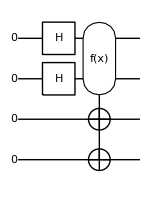

```mathematica
cc={1,2};
tt={3,4};
qc=QuantumCircuit[Ket[S@Join[cc,tt]],S[cc,6],Oracle[f,S@cc,S@tt]]
```

The output state is an entangled state (unless the classical oracle f is constant).

```mathematica
out=ExpressionFor[qc]
```

1/2 0_S_10_S_21_S_31_S_4+1/2 0_S_11_S_21_S_30_S_4+1/2 1_S_10_S_20_S_31_S_4+1/2 1_S_11_S_20_S_30_S_4

To make clearer the copies made tot the ancillary register, it may be useful to rewrite the state vector in a form that distinguishes the native and ancillary register.

```mathematica
KetFactor[out,S@cc]
```

0_S_10_S_2⊗(1/2 1_S_31_S_4)+0_S_11_S_2⊗(1/2 1_S_30_S_4)+1_S_10_S_2⊗(1/2 0_S_31_S_4)+1_S_11_S_2⊗(1/2 0_S_30_S_4)

### Conditional Phase Shifts

This is an interesting twist of quantum oracle and provides a way to implement the phase shifts conditioned on a given function f. It is useful, for example, in the Deutsch-Jozsa algorithm, Bernstein-Vazirani algorithm, and quantum search algorithm.

The classical oracle mark the solutions, {0,0}=1 and {1,1}=1 in this particular case.

```mathematica
Clear[f];
f[{0,0}]=1;
f[{0,1}]=0;
f[{1,0}]=0;
f[{1,1}]=1;
```

This quantum circuit model implements the desired mapping.

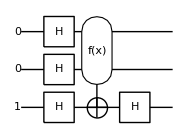

```mathematica
cc={1,2};
tt={3};
ct=Join[cc,tt];
qc=QuantumCircuit[Ket[S[tt]->1,S[ct]],
S[ct,6],Oracle[f,S@cc,S@tt],S[tt,6]]
```

```mathematica
out=ExpressionFor[qc]
```

-1/2 0_S_10_S_21_S_3+1/2 0_S_11_S_21_S_3+1/2 1_S_10_S_21_S_3-1/2 1_S_11_S_21_S_3

Check the result.

```mathematica
in=Basis[S@cc];
ff=f/@IntegerDigits[Range[0,2^2-1],2,2];
Thread[in->Power[-1,ff]]
```

{0_S_10_S_2→-1,0_S_11_S_2→1,1_S_10_S_2→1,1_S_11_S_2→-1}

```mathematica
new=in.Power[-1,ff]/2
```

1/2 (-0_S_10_S_2+0_S_11_S_2+1_S_10_S_2-1_S_11_S_2)

| Related Guides
▪Quantum Information Systems

| Related Tech Notes
▪Quantum Decision Algorithms
▪Quantum Algorithms
▪Quantum Information Systems with Q3

| Related Links
▪M. Nielsen and I. L. Chuang (2022)https://doi.org/10.1017/CBO9780511976667, Quantum Computation and Quantum Information (Cambridge University Press).
▪Mahn-Soo Choi (2022)https://doi.org/10.1007/978-3-030-91214-7, A Quantum Computation Workbook (Springer).